# Hints for a gravitational constant transition in Tully - Fisher data - G. Alestas, I. Antoniou and L. Perivolaropoulos - Figure 3, 4

## General Settings

### Setting the Environment

```mathematica
SetDirectory[NotebookDirectory[]]
Off[General::obspkg,First::nofirst,InterpolatingFunction::dmval];
```

D:\Games\Dropbox\Research\tully-fisher-Geff\giorgos-math-files

### Importing Data

```mathematica
data5=Import["Data//Lel19a.dat","Data"];
ndat5=Length[data5];
data6=Import["Data//Lel19b.dat","Data"];
ndat6=Length[data6];
```

### Definitions of Functions

```mathematica
(* -----Function that draws redshifts from the SIMBAD catalogue----- *)
fullname[object_]:=Module[{string},If[Head[object]===Entity,string=object["Name"],string=object];StringReplace[ToString[string,CharacterEncoding->None],(a___~~"\\["~~b__~~"]"~~c___):>a~~b~~c]]

SIMBADredshifts[id_]/;(Head[id]===Entity||StringQ[id]):=Module[
{
import,query,root="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=",
id2=fullname[id]
},
query=URLEncode[StringTemplate["SELECT rvz_redshift FROM BASIC WHERE main_id = '`id`';"][<|"id"->id2|>]];
import=Import[root~~query,"TSV"];
If[import===$Failed,Return[imbad]];
First@Flatten@Rest[import]]

SIMBADdistances[id_]/;(Head[id]===Entity||StringQ[id]):=Module[
{
import,query,root="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=",
id2=fullname[id]
},
query=URLEncode[StringTemplate["SELECT basic.OID FROM basic JOIN ident ON oidref = oid WHERE id = '`id`';"][<|"id"->id2|>]];
import=Import[root~~query,"TSV"];
If[import===$Failed,Return[imbad]];
oid=fullname[First@Flatten@Rest[import]];
If[oid=="First[{}]",0,query=URLEncode[StringTemplate["SELECT dist FROM mesDistance WHERE oidref= '`oid`';"][<|"oid"->oid|>]];
import=Import[root~~query,"TSV"];
If[import===$Failed,Return[imbad]];
First@Flatten@Rest[import]]]
```

## Figure 3

### Analysis for Dataset “Lelli_2019” (arXiv: 1901.05966 - SPARC)

```mathematica
tb2=Table[{data5[[i,2]],data5[[i,4]],data5[[i,6]]},{i,1,ndat5}];
tb16berr=Table[{Around[data5[[i,2]],data5[[i,3]]],Around[data5[[i,4]],data5[[i,5]]],data5[[i,6]]},{i,1,ndat5}];
```

```mathematica
plall=Plot[3.7x+2.287==0,{x,0,5},PlotStyle->RGBColor["#2ab7ca"]];
plalla=Plot[{3.71x+2.31==0,3.69x+2.257==0},{x,0,5},Filling->{1->{{2},{LightBlue}}},PlotRange-> {{1.4,2.7},{6.5,13}},PlotStyle->{{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];

pl91=Plot[3.46x+2.854==0,{x,0,5},PlotStyle->RGBColor["#2ab7ca"]];
pl91a=Plot[{3.43x+2.78==0,3.49x+2.92==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{1->{{2},{LightBlue}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_rot (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
pl92=Plot[3.586x+2.46==0,{x,0,5},PlotStyle->{RGBColor["#ff3377"]}];
pl92a=Plot[{3.546x+2.381==0,3.626x+2.541==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{1->{{2},{LightRed}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];

pl181=Plot[3.548x+2.677==0,{x,0,5},PlotStyle->RGBColor["#2ab7ca"]];
pl181a=Plot[{(3.548+0.02)x+(2.677+0.05)==0,(3.548-0.02)x+(2.677-0.05)==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{1->{{2},{LightBlue}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_rot (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
pl182=Plot[3.59x+2.467==0,{x,0,5},PlotStyle->{RGBColor["#ff3377"]}];
pl182a=Plot[{(3.59+0.02)x+(2.467+0.06)==0,(3.59-0.02)x+(2.467-0.06)==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{1->{{2},{LightRed}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];

pl401=Plot[3.28x+3.318==0,{x,0,5},PlotStyle->RGBColor["#2ab7ca"]];
pl401a=Plot[{(3.28+0.14)x+(3.318+0.8)==0,(3.28-0.14)x+(3.318-0.8)==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{1->{{2},{LightBlue}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_rot (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
pl402=Plot[3.68x+2.327==0,{x,0,5},PlotStyle->{RGBColor["#ff3377"]}];
pl402a=Plot[{(3.68+0.14)x+(2.327+0.6)==0,(3.68-0.14)x+(2.327-0.6)==0},{x,0,5},PlotStyle->{{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{1->{{2},{LightRed}}},PlotRange-> {{1.4,2.7},{6.5,13}}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];


disttab16=Table[tb2[[i,3]],{i,1,ndat5}];
maxdist16=Max[disttab16];
mindist16=Min[disttab16];
nsplt=20;
ddist16=(maxdist16-mindist16)/nsplt;


tb16aerr=Table[{tb16berr[[i,1]],tb16berr[[i,2]]},{i,1,Length[tb16berr]}];
tb16=Table[{tb2[[i,1]],tb2[[i,2]]},{i,1,Length[tb2]}];
lm16=LinearModelFit[tb16,x,x,ConfidenceLevel->.68];
plallin=Plot[{3.7x+2.287==0,3.71x+2.31==0,3.69x+2.257==0},{x,0,0.04},PlotRange->{2.25,2.45},PlotStyle->{{RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{2->{{3},{LightBlue}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
pla0=ListPlot[tb16aerr,PlotRange-> {{1.4,2.7},{6.5,13}},PlotStyle->{PointSize->Medium,RGBColor["#2ab7ca"]}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
pl0=Show[{plalla,pla0,plall},Epilog->{Inset[plallin,Scaled[{0.75,0.25}]]},Frame->{{True,True},{False,True}}];
```

```mathematica
i=1.42; (* Distance cut-off point *)
dsplt16=i ddist16
tbs16err=Select[tb16berr,#[[3]]<dsplt16 &];
tbl16err=Select[tb16berr,#[[3]]>dsplt16 &];
tbs16aerr=Table[{tbs16err[[i,1]],tbs16err[[i,2]]},{i,1,Length[tbs16err]}];
tbl16aerr=Table[{tbl16err[[i,1]],tbl16err[[i,2]]},{i,1,Length[tbl16err]}];
tbs16=Select[tb2,#[[3]]<dsplt16 &];
tbl16=Select[tb2,#[[3]]>dsplt16 &];
tbs16a=Table[{tbs16[[i,1]],tbs16[[i,2]]},{i,1,Length[tbs16]}];
tbl16a=Table[{tbl16[[i,1]],tbl16[[i,2]]},{i,1,Length[tbl16]}];
lms16=LinearModelFit[tbs16a,x,x,ConfidenceLevel->.68]
lml16=LinearModelFit[tbl16a,x,x,ConfidenceLevel->.68]
plins=Plot[{3.586x+2.46==0,3.546x+2.381==0,3.626x+2.541==0},{x,0,0.04},PlotRange->{2.2,3.2},PlotStyle->{{RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{2->{{3},{LightRed}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
plinl=Plot[{3.46x+2.854==0,3.43x+2.78==0,3.49x+2.92==0},{x,0,0.04},PlotStyle->{{RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{2->{{3},{LightBlue}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
pl9in=Show[plins,plinl];
pla1=ListPlot[tbs16aerr,PlotRange-> {{1.4,2.7},{6.5,13}},PlotStyle->{PointSize->Medium, RGBColor["#ff3377"]}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
plb1=ListPlot[tbl16aerr,PlotStyle->{PointSize->Medium,RGBColor["#2ab7ca"]}];
pl1=Show[{pl91a,pl92a,pla1,plb1,pl91,pl92},Prolog->{Inset[pl9in,Scaled[{0.75,0.25}]]},Epilog->Inset[Framed["D_c = 9 Mpc"],Scaled[{0.12,0.85}],BaseStyle -> {FontFamily->"Times",25}],Frame->{{False,True},{False,True}}];
```

9.00422

FittedModel[2.7253+3.44889 x]

FittedModel[3.12633+3.33268 x]

```mathematica
i=2.84; (* Distance cut-off point *)
dsplt16=i ddist16
tbs16err=Select[tb16berr,#[[3]]<dsplt16 &];
tbl16err=Select[tb16berr,#[[3]]>dsplt16 &];
tbs16aerr=Table[{tbs16err[[i,1]],tbs16err[[i,2]]},{i,1,Length[tbs16err]}];
tbl16aerr=Table[{tbl16err[[i,1]],tbl16err[[i,2]]},{i,1,Length[tbl16err]}];
tbs16=Select[tb2,#[[3]]<dsplt16 &];
tbl16=Select[tb2,#[[3]]>dsplt16 &];
tbs16a=Table[{tbs16[[i,1]],tbs16[[i,2]]},{i,1,Length[tbs16]}];
tbl16a=Table[{tbl16[[i,1]],tbl16[[i,2]]},{i,1,Length[tbl16]}];
(*lms16=LinearModelFit[tbs16a,x,x,ConfidenceLevel->.68]
lml16=LinearModelFit[tbl16a,x,x,ConfidenceLevel->.68]*)
plins=Plot[{3.59x+2.467==0,(3.59+0.02)x+(2.467+0.06)==0,(3.59-0.02)x+(2.467-0.06)==0},{x,0,0.04},PlotRange->{2.2,3.2},PlotStyle->{{RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{2->{{3},{LightRed}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
plinl=Plot[{3.548x+2.677==0,(3.548+0.02)x+(2.677+0.05)==0,(3.548-0.02)x+(2.677-+0.05)==0},{x,0,0.04},PlotStyle->{{RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{2->{{3},{LightBlue}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
pl17in=Show[plins,plinl];
pla2=ListPlot[tbs16aerr,PlotRange->{{1.4,2.7},{6.5,13}},PlotStyle->{PointSize->Medium, RGBColor["#ff3377"]}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
plb2=ListPlot[tbl16aerr,PlotStyle->{PointSize->Medium, RGBColor["#2ab7ca"]}];
(*plc2=Plot[lms16[x],{x,0,3.5},PlotStyle->{Dashed,Red}]; (* Plot linear fit for smaller distances *)
pld2=Plot[lml16[x],{x,0,3.5},PlotStyle->{Dashed,Blue}];(* Plot linear fit for larger distances *)*)
pl2=Show[{pl181a,pl182a,pla2,plb2,pl181,pl182},Prolog->{Inset[pl17in,Scaled[{0.75,0.25}]]},Epilog->Inset[Framed["D_c = 17 Mpc"],Scaled[{0.12,0.85}],BaseStyle -> {FontFamily->"Times",25}]];
```

18.0084

```mathematica
i=6.3; (* Distance cut-off point *)
dsplt16=i ddist16
tbs16err=Select[tb16berr,#[[3]]<dsplt16 &];
tbl16err=Select[tb16berr,#[[3]]>dsplt16 &];
tbs16aerr=Table[{tbs16err[[i,1]],tbs16err[[i,2]]},{i,1,Length[tbs16err]}];
tbl16aerr=Table[{tbl16err[[i,1]],tbl16err[[i,2]]},{i,1,Length[tbl16err]}];
tbs16=Select[tb2,#[[3]]<dsplt16 &];
tbl16=Select[tb2,#[[3]]>dsplt16 &];
tbs16a=Table[{tbs16[[i,1]],tbs16[[i,2]]},{i,1,Length[tbs16]}];
tbl16a=Table[{tbl16[[i,1]],tbl16[[i,2]]},{i,1,Length[tbl16]}];
lms16=LinearModelFit[tbs16a,x,x,ConfidenceLevel->.68]
lml16=LinearModelFit[tbl16a,x,x,ConfidenceLevel->.68]
plins=Plot[{3.68x+2.327==0,(3.68+0.14)x+(2.327+0.6)==0,(3.68-0.14)x+(2.327-0.6)==0},{x,0,0.04},PlotRange->{1.5,4},PlotStyle->{{RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]},{Dashed,RGBColor["#ff3377"]}},Filling->{2->{{3},{LightRed}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
plinl=Plot[{3.28x+3.318==0,(3.28+0.14)x+(3.318+0.8)==0,(3.28-0.14)x+(3.318-0.8)==0},{x,0,0.04},PlotRange->{1.5,4},PlotStyle->{{RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]},{Dashed,RGBColor["#2ab7ca"]}},Filling->{2->{{3},{LightBlue}}}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->400, FrameStyle -> Directive[Black, Thick]];
pl40in=Show[plinl,plins];
pla3=ListPlot[tbs16aerr,PlotRange-> {{1.4,2.7},{6.5,13}},PlotStyle->{PointSize->Medium,RGBColor["#ff3377"]}, Frame->True,FrameLabel->{"log V_f (km s^-1)","log M_b (M_☉)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
plb3=ListPlot[tbl16aerr,PlotStyle->{PointSize->Medium,RGBColor["#2ab7ca"]}];
plc3=Plot[lms16[x],{x,1.4,3.5},PlotStyle->{Dashed,Red}]; (* Plot linear fit for smaller distances *)
pld3=Plot[lml16[x],{x,1.4,3.5},PlotStyle->{Dashed,Blue}];(* Plot linear fit for larger distances *)
pl3=Show[pl401a,pl402a,pla3,plb3,pl401,pl402,Epilog->{Inset[pl40in,Scaled[{0.75,0.25}]]},Prolog->Inset[Framed["D_c = 40 Mpc"],Scaled[{0.12,0.85}],BaseStyle -> {FontFamily->"Times",25}],Frame->{{False,True},{True,True}}];
```

39.9483

FittedModel[2.67207+3.5179 x]

FittedModel[3.27193+3.29222 x]

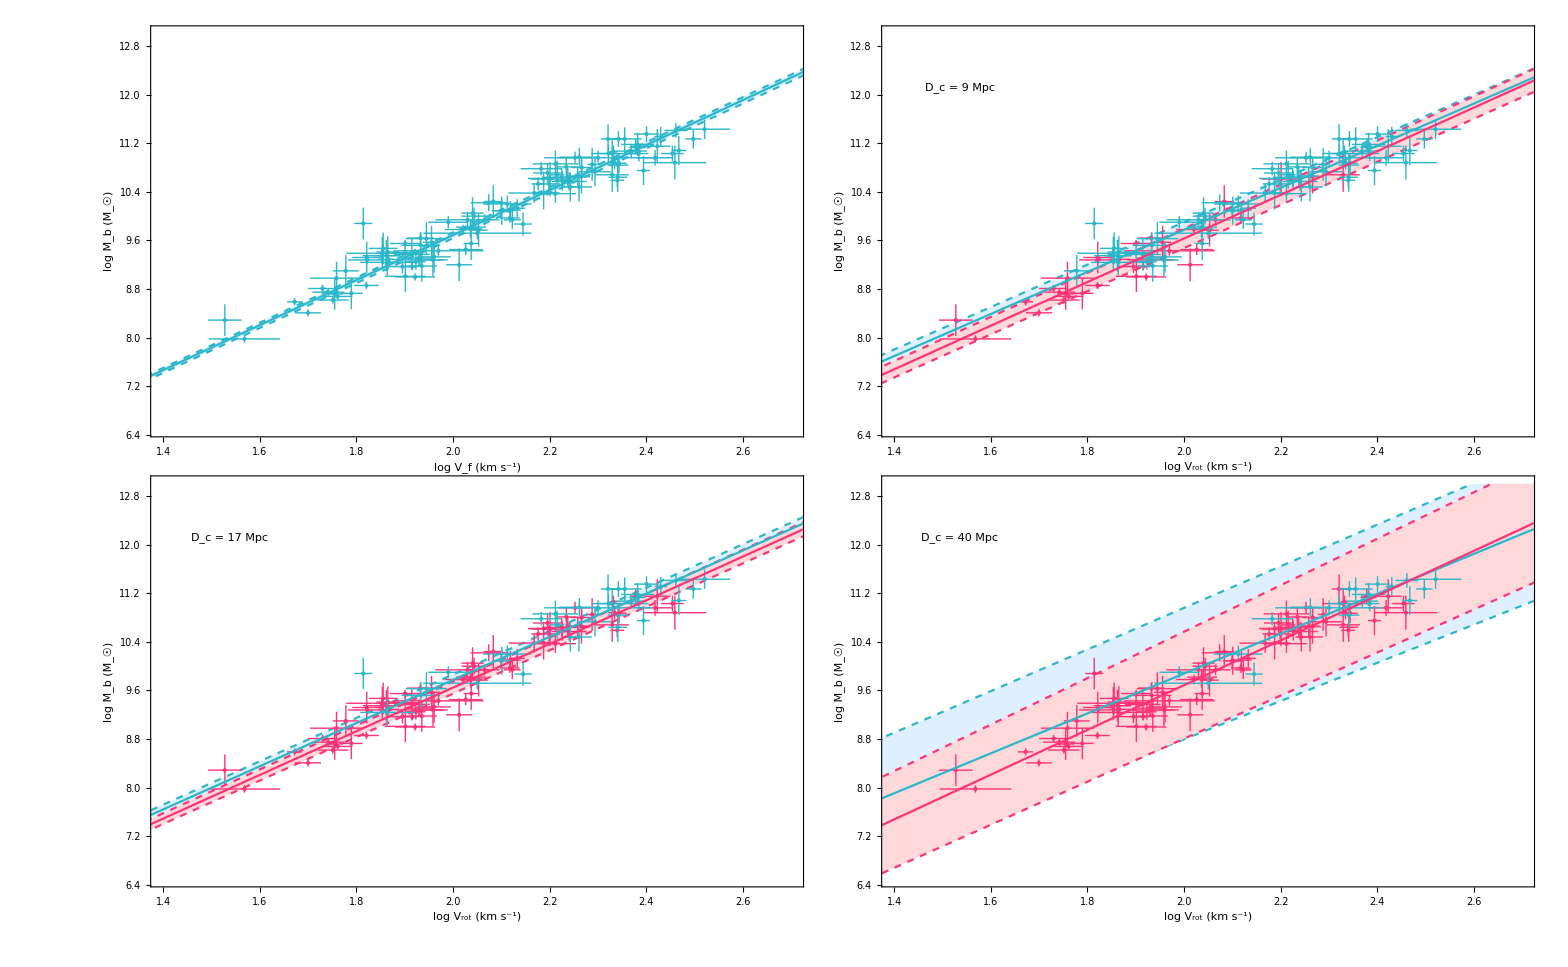

```mathematica
pl=GraphicsGrid[{{pl0,pl1},{pl2,pl3}},Spacings->{-114,-72},ImageSize->1900]
```

```mathematica
Export[NotebookDirectory[]<>"fig3.pdf",pl,ImageResolution->1000];
```

## Figure 4

### Analysis for Dataset “Lelli_2019” (arXiv: 1901.05966 - SPARC)

FittedModel[-0.000719512+0.000240977 x]

{{7.70.4,0.001134},{4.040.20,0.001248},{7.52.3,0.002485},{4.250.21,0.00065},{15.5.,0.003119},{29.7.,0.007732},{13.4.,0.00380989},{61.9.,0.0151918},{3.910.20,0.00016},{100.10.,0.02376},{7.30.4,0.00183696},{2.110.11,0.00043039},{18.450.20,0.002812},{3.700.19,0.000530508},{21.5.,0.00544793},{2.080.10,0.000487122},{81.8.,0.019187},{9.90.5,0.00176277},{11.43.4,0.0020903},{37.9.,0.00927978},{3.160.16,0.00043},{9.80.5,0.00136428},{14.11.4,0.0019},{6.62.0,0.001855},{4.060.20,0.00155963},{3.580.18,0.00004},{68.10.,0.01591},{1.330.07,0.00134517},{13.81.4,0.00227},{7.72.3,0.00266272},{18.02.5,0.002872},{3.210.17,0.000783876},{18.02.5,0.00235},{18.02.5,0.00302},{18.02.5,0.003242},{18.02.5,0.00302968},{18.02.5,0.002665},{18.02.5,0.003509},{18.02.5,0.002799},{23.72.3,0.003496},{18.02.5,0.00304005},{18.02.5,0.002722},{18.02.5,0.00216483},{18.02.5,0.002502},{18.02.5,0.002515},{18.02.5,0.003582},{18.02.5,0.002955},{18.02.5,0.002608},{18.02.5,0.00309359},{18.02.5,0.003419},{7.310.20,0.002719},{16.91.5,0.003212},{16.5.,0.00283863},{9.90.5,0.001678},{40.10.,0.0085},{7.12.1,0.0010107},{17.30.9,0.002225},{50.350.20,0.008372},{17.5.,0.00277859},{128.13.,0.02999},{6.260.31,0.000143433},{51.10.,0.011438},{5.51.7,0.00015},{14.71.5,0.002732},{14.40.7,0.00350523},{65.10.,0.015124},{13.4.,0.002131},{5.270.10,0.00054},{10.53.1,0.00194657},{69.10.,0.016514},{81.8.,0.0197637},{65.10.,0.015277},{17.5.,0.003446},{50.10.,0.0119716},{29.7.,0.006151},{21.5.,0.0040061},{12.590.20,0.001868},{9.62.9,0.001731},{13.4.,0.002297},{23.6.,0.004306},{21.5.,0.00387},{6.21.9,0.001785},{8.62.6,0.002064},{18.02.5,0.00255},{12.4.,0.002148},{89.9.,0.02121},{18.02.5,0.00325421},{29.7.,0.005971},{21.5.,0.003929},{18.02.5,0.002715},{18.02.5,0.003045},{18.02.5,0.00349575},{18.02.5,0.002628},{18.02.5,0.00361},{20.6.,0.0034},{6.870.34,0.00088},{8.42.5,0.001801},{4.740.24,0.00106},{4.71.4,0.00199},{8.12.4,0.001788},{6.500.33,0.001348},{4.70.5,0.000677},{6.72.0,0.001214},{39.10.,0.00833},{84.8.,0.01982},{57.11.,0.01282},{15.5.,0.002378},{79.12.,0.017942},{17.5.,0.003166},{101.10.,0.02413},{9.82.9,0.001408},{4.350.22,0.000834},{0.980.05,-0.000434}}

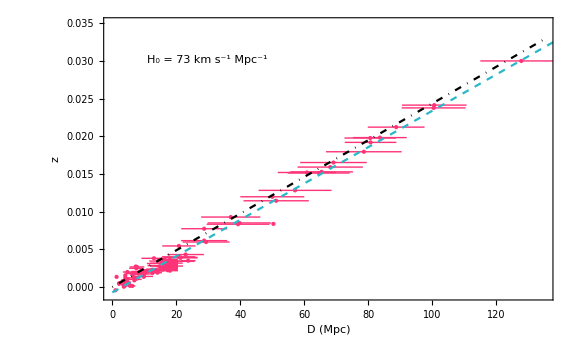

```mathematica
colorFun=Function[{x,y},Blend[{{Min[altitude],LightRed},{Max[altitude],RGBColor["#ff3377"]}},Norm[{x/100,y/100}]]];
MapThread[{colorFun[#1]}&{altitude}];
tbzd=Table[{data6[[i,6]],data6[[i,8]]},{i,1,ndat6}];
lmzd=LinearModelFit[tbzd,x,x,ConfidenceLevel->.68]
pllmzd=Plot[lmzd[x],{x,0,150},PlotStyle->{Dashed,,RGBColor["#2ab7ca"]}];
tbzderr=Table[{Around[data6[[i,6]],data6[[i,7]]],data6[[i,8]]},{i,1,ndat6}]
plzd=ListPlot[tbzderr, ImageSize->Large,PlotStyle->{PointSize->Medium,RGBColor["#ff3377"](*ColorFunction->colorFun,ColorFunctionScaling->False,IntervalMarkersStyle->{RGBColor["#ff3377"],Blend[{{Min[altitude],LightRed},{Max[altitude],RGBColor["#ff3377"]}}],Norm[{x/100,y/100}]*)}, Frame->True,FrameLabel->{"D (Mpc)","z"},PlotRange->{{0,135},{-0.001,0.035}},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->900, FrameStyle -> Directive[Black, Thick]];
z[D_]:=2.435 10^-4 D
plh0=Plot[z[D],{D,0,135},PlotStyle->{Black,DotDashed}];
plzdall=Show[plzd,plh0,pllmzd,Epilog->Inset[Framed["H_0 = 73 km s^-1 Mpc^-1"],Scaled[{0.23,0.85}],BaseStyle -> {FontFamily->"Times",18}]]
```

```mathematica
Export[NotebookDirectory[]<>"fig4.pdf",plzdall,ImageResolution->1000];
```